```mathematica
SetDirectory[NotebookDirectory[]];
```

### Test BR_aa=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst.dat"];
data[[1]]
```

{1000.,9.999999999999999988×10^-15,0.,0.752507899999957264,0.0000183792399999989577,0.,7.75538032999956623×10^-6,0.06185800999999648,8.10474899999979646×10^-15,4.08745259999976775×10^-10,0.,0.,0.752573399999957204,0.0000179224799999989787,0.,7.83537462999956215×10^-6,0.0618417999999964843,2.6269949999998786×10^-14,4.37593159999975133×10^-10,0.,0.,0.752442499999957271,0.0000188398199999989295,0.,7.68602713999957009×10^-6,0.0618741799999964828,1.26003800000016864×10^-15,3.82641399999978251×10^-10,0.}

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
plotDataDoverH=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data],Map[DoverHhigh,data],Map[DoverHlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

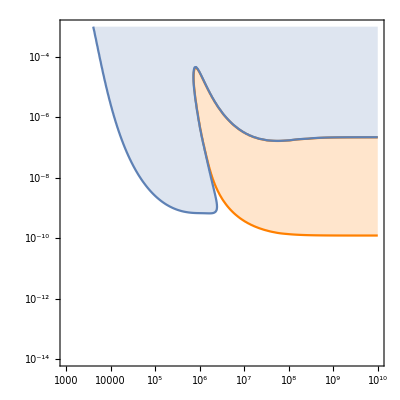

```mathematica
ListContourPlot[plotDataDoverH,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange];
ListContourPlot[plotDataDoverH,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger];
Show[plt1,plt2]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

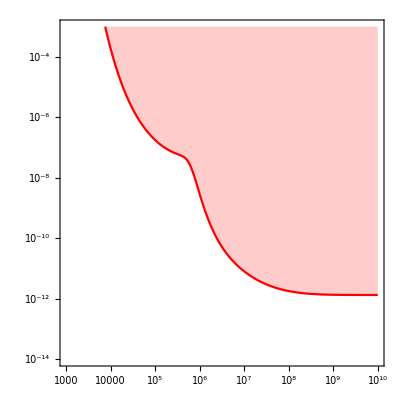

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

```mathematica
He4mean[data_]:=4*data[[8]];
He4high[data_]:=4*data[[17]];
He4low[data_]:=4*data[[26]];
He4obs=2.45*10^-1;
He4err=0.01*10^-1;
deltaHe4[mean_,high_,low_]:=(mean-He4obs)/Sqrt[sigmaTh[mean,high,low]^2+He4err^2];
plotDataHe4=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe4,Map[He4mean,data],Map[He4high,data],Map[He4low,data]]]];
```

General::munfl: 0.-1.97626258336498618×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.+1.97626258336498618×10^-323 is too small to represent as a normalized machine number; precision may be lost.

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

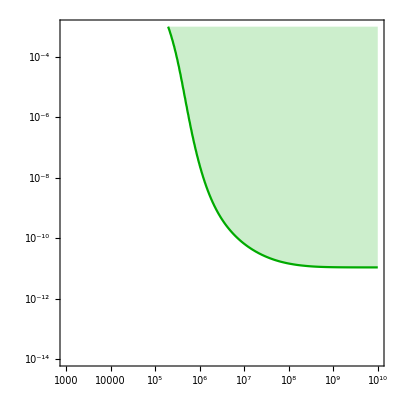

```mathematica
ListContourPlot[plotDataHe4,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt4=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Darker[Green]]
```

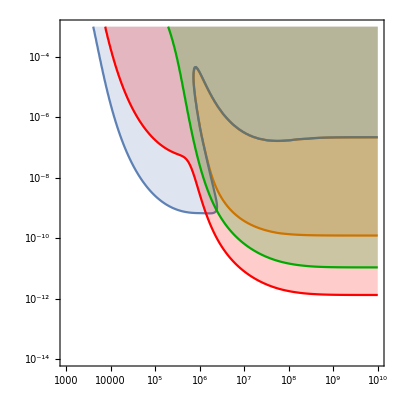

```mathematica
Show[plt1,plt2,plt3,plt4]
```

### Test BR_ee=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst_ee.dat"];
data[[1]]
```

$Aborted

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

data⟦1⟧

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
```

```mathematica
dataDoverHmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,5]]/data[[i,4]]]},{i,1,Length[data]}];
dataHe3overDmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,7]]/data[[i,5]]]},{i,1,Length[data]}];
dataDoverHhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,14]]/data[[i,13]]]},{i,1,Length[data]}];
dataHe3overDhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,16]]/data[[i,14]]]},{i,1,Length[data]}];dataDoverHlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,23]]/data[[i,22]]]},{i,1,Length[data]}];
dataHe3overDlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,25]]/data[[i,23]]]},{i,1,Length[data]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
dataHe3overDlow[[20000;;20020]]
```

{{1.492462311557788868,-2.99999999999999999,1.73614129918733221},{1.507537688442210945,-14.000000000000000001,-0.389374803622645004},{1.507537688442210945,-13.94472361809045145,-0.389374798609256442},{1.507537688442210945,-13.88944723618090471,-0.389374793803672847},{1.507537688442210945,-13.83417085427135617,-0.389374788195775617},{1.507537688442210945,-13.77889447236180942,-0.389374782190557976},{1.507537688442210945,-13.72361809045226088,-0.389374774374201784},{1.507537688442210945,-13.6683417085427141,-0.389374766364638177},{1.507537688442210945,-13.61306532663316561,-0.38937475715308054},{1.507537688442210945,-13.55778894472361883,-0.38937474633563254},{1.507537688442210945,-13.50251256281407028,-0.389374734520943318},{1.507537688442210945,-13.447236180904521743,-0.389374720699743977},{1.507537688442210945,-13.391959798994974989,-0.389374705076972253},{1.507537688442210945,-13.336683417085426455,-0.389374687249801321},{1.507537688442210945,-13.281407035175879727,-0.389374667019508128},{1.507537688442210945,-13.226130653266331167,-0.38937464459067929},{1.507537688442210945,-13.170854271356784442,-0.389374618551724693},{1.507537688442210945,-13.11557788944723588,-0.38937458850252747},{1.507537688442210945,-13.060301507537689154,-0.389374554851835903},{1.507537688442210945,-13.005025125628140619,-0.389374517200357168},{1.507537688442210945,-12.94974874371859388,-0.38937447413870929}}

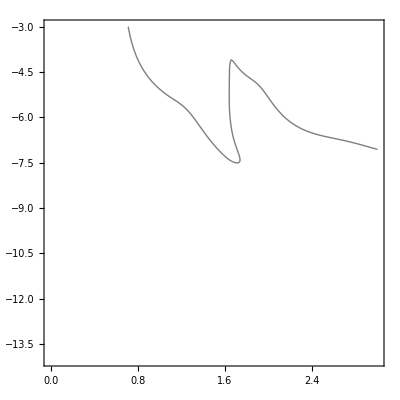

```mathematica
ListContourPlot[dataDoverHhigh,Contours->{-5},ContourShading->Log10[DoverHobs+2*DoverHerr]]
```

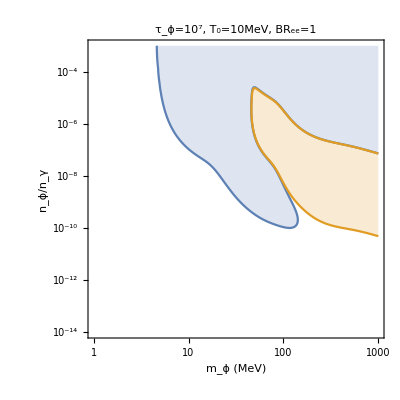

```mathematica
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
ListContourPlot[dataDoverHhigh,Contours->{Log10[DoverHobs+2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
ListContourPlot[dataDoverHlow,Contours->{Log10[DoverHobs-2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%,%%%%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"m_ϕ (MeV)","n_ϕ/n_γ"},PlotLabel->"τ_ϕ=10^7, T_0=10MeV, BR_ee=1"]
```

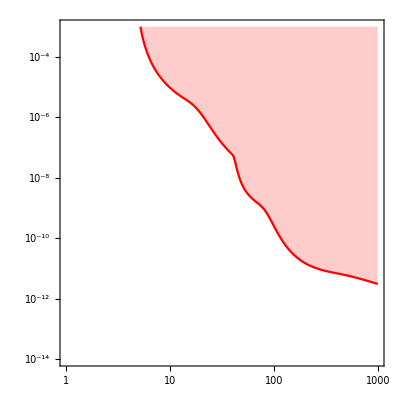

```mathematica
He3overDobs=0.83;
He3overDerr=0.15;
ListContourPlot[dataHe3overDhigh,Contours->{Log10[He3overDobs+2*He3overDerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

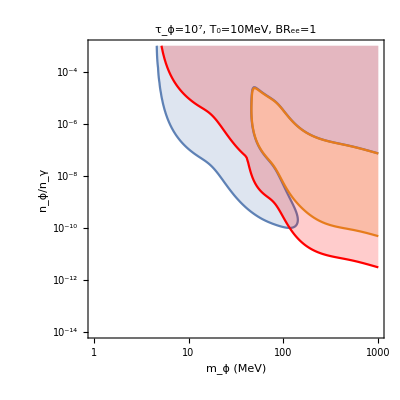

```mathematica
Show[plt1,plt2]
```

### Our Model

```mathematica
(*Quit[]*)
```

```mathematica
importData={Import["~/prj/acropolis/MD1_100_MD2_105_MZp_300.dat"],Import["~/prj/acropolis/MD1_100_MD2_110_MZp_300.dat"],Import["~/prj/acropolis/MD1_100_MD2_120_MZp_300.dat"]};
importDataP2={Import["~/prj/acropolis/MD1_50_MD2_55_MZp_150.dat"],Import["~/prj/acropolis/MD1_50_MD2_60_MZp_150.dat"],Import["~/prj/acropolis/MD1_50_MD2_65_MZp_150.dat"]};
importDataP3={Import["~/prj/acropolis/MD1_500_MD2_505_MZp_1500.dat"],Import["~/prj/acropolis/MD1_500_MD2_525_MZp_1500_combined.dat"],Import["~/prj/acropolis/MD1_500_MD2_550_MZp_1500.dat"],Import["~/prj/acropolis/MD1_500_MD2_600_MZp_1500.dat"]};
```

```mathematica
data=Table[Block[{data=importData[[k]]},Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}]],{k,1,Length[importData]}];

dataP2=Table[Block[{data=importDataP2[[k]]},Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}]],{k,1,Length[importDataP2]}];

dataP3=Table[Block[{data=importDataP3[[k]]},Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}]],{k,1,Length[importDataP3]}];
```

```mathematica
dataP3
```

{{{-4.,-5.,0.,0.752507541176354322,0.0000183792312360974541,0.,7.75537663194736309×10^-6,0.0618579805038091124,8.10474513535541171×10^-15,4.08745065095116825×10^-10,0.,0.,0.752573041145121469,0.0000179224714538975403,0.,7.83537089380311742×10^-6,0.0618417705115386421,2.62699374735145914×10^-14,4.37592951339369292×10^-10,0.,0.,0.752442141207539494,0.0000188398110164758468,0.,7.6860234750175356×10^-6,0.061874150496098658,1.26003739916719968×10^-15,3.82641217542404359×10^-10,0.},117,{-0.75,-4.75,0.,0.752507899999914409,0.0000183792399999958237,0.,7.75538032999912746×10^-6,0.0618580099999929689,8.1047489999990786×10^-15,4.08745259999469352×10^-10,0.,0.,0.75257339999991435,3,0.0618417999999929732,2.62699499999970158×10^-14,4.37593159999430279×10^-10,0.,0.,0.752442499999914416,0.0000188398199999957176,0.,7.6860271399991381×10^-6,0.0618741799999929648,1.26003799999985685×10^-15,3.82641399999504535×10^-10,0.}},2,{{1}}}
 |  |  |  |

```mathematica
Dimensions[data]
For[i=1,i<Length[data]+1,i++,Print[Dimensions[data[[i]]]]]
```

{3}

{15,29}

{10,29}

{3,29}

```mathematica
(*data=importData[[2]];
data=Table[{data[[i,1]],data[[i,2]],data[[i,3]],data[[i,6]],data[[i,9]],data[[i,12]],data[[i,15]],data[[i,18]],data[[i,21]],data[[i,24]],data[[i,27]],data[[i,4]],data[[i,7]],data[[i,10]],data[[i,13]],data[[i,16]],data[[i,19]],data[[i,22]],data[[i,25]],data[[i,28]],data[[i,5]],data[[i,8]],data[[i,11]],data[[i,14]],data[[i,17]],data[[i,20]],data[[i,23]],data[[i,26]],data[[i,29]]},{i,1,Length[data]}];
Dimensions[data]*)
```

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
```

```mathematica
plotDataDoverH=Table[Transpose[AppendTo[Transpose[data[[k]]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data[[k]]],Map[DoverHhigh,data[[k]]],Map[DoverHlow,data[[k]]]]]],{k,1,Length[importData]}];
plotDataDoverHP2=Table[Transpose[AppendTo[Transpose[dataP2[[k]]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,dataP2[[k]]],Map[DoverHhigh,dataP2[[k]]],Map[DoverHlow,dataP2[[k]]]]]],{k,1,Length[importDataP2]}];
plotDataDoverHP3=Table[Transpose[AppendTo[Transpose[dataP3[[k]]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,dataP3[[k]]],Map[DoverHhigh,dataP3[[k]]],Map[DoverHlow,dataP3[[k]]]]]],{k,1,Length[importDataP3]}];
```

Set::setps: Transpose[data⟦k⟧] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::setps: Transpose[dataP2⟦k⟧] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::setps: Transpose[dataP3⟦k⟧] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

```mathematica
plotDataDoverH
```

{{{-4.,-5.,-1.48908},{-4.,-4.5,-1.48908},{-4.,-4.,-1.49082},{-4.,-3.5,-1.49583},{-4.,-3.,-1.48914},{-3.5,-5.,-1.48908},{-3.5,-4.5,-1.48932},{-3.5,-4.,-1.49},{-3.5,-3.5,-1.48908},{-3.,-5.,-1.48911},{-3.,-4.5,-1.48922},{-3.,-4.,-1.48908},{-2.5,-5.,-1.4891},{-2.5,-4.5,-1.48908},{-2.,-5.,-1.48908}},{{-4.,-5.,-3.24166},{-4.,-4.5,-9.24684},{-4.,-4.,-1.94664},{-4.,-3.5,-1.48908},{-3.5,-5.,-2.39555},{-3.5,-4.5,-1.57247},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4973},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}},{{-4.,-5.,-11.5643},{-4.,-4.5,-1.49668},{-3.5,-5.,-1.48946}}}

```mathematica
plotDataDoverHP2
```

{{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}},{{-4.,-5.,-2.39648},{-4.,-4.5,-1.5254},{-3.5,-5.,-1.49154}},{{-4.,-5.,-1.54748},{-4.,-4.5,-1.48908},{-3.5,-5.,-1.48908}}}

```mathematica
plotDataDoverHP3
```

{{{-4.,-5.,-1.48908},{-4.,-4.75,-1.48908},{-4.,-4.5,-1.48908},{-4.,-4.25,-1.48908},{-4.,-4.,-1.48908},{-4.,-3.75,-1.48908},{-4.,-3.5,-1.48908},{-4.,-3.25,-1.48908},{-4.,-3.,-1.48936},{-4.,-2.75,-1.50001},{-4.,-2.5,-1.52586},{-4.,-2.25,-1.55193},{-4.,-2.,-1.52703},{-4.,-1.75,-1.49195},{-4.,-1.5,-1.48909},{-3.75,-5.,-1.48908},{-3.75,-4.75,-1.48908},{-3.75,-4.5,-1.48908},{-3.75,-4.25,-1.48908},{-3.75,-4.,-1.48908},{-3.75,-3.75,-1.48908},{-3.75,-3.5,-1.48908},{-3.75,-3.25,-1.48919},{-3.75,-3.,-1.49346},{-3.75,-2.75,-1.50376},{-3.75,-2.5,-1.51385},{-3.75,-2.25,-1.50362},{-3.75,-2.,-1.49005},{-3.75,-1.75,-1.48908},{-3.5,-5.,-1.48908},{-3.5,-4.75,-1.48908},{-3.5,-4.5,-1.48908},{-3.5,-4.25,-1.48908},{-3.5,-4.,-1.48908},{-3.5,-3.75,-1.48908},{-3.5,-3.5,-1.48912},{-3.5,-3.25,-1.49087},{-3.5,-3.,-1.4951},{-3.5,-2.75,-1.4992},{-3.5,-2.5,-1.49504},{-3.5,-2.25,-1.48947},{-3.5,-2.,-1.48908},{-3.25,-5.,-1.48908},{-3.25,-4.75,-1.48908},{-3.25,-4.5,-1.48908},{-3.25,-4.25,-1.48908},{-3.25,-4.,-1.48908},{-3.25,-3.75,-1.4891},{-3.25,-3.5,-1.48983},{-3.25,-3.25,-1.49165},{-3.25,-3.,-1.49346},{-3.25,-2.75,-1.49174},{-3.25,-2.5,-1.48927},{-3.25,-2.25,-1.48908},{-3.,-5.,-1.48908},{-3.,-4.75,-1.48908},{-3.,-4.5,-1.48908},{-3.,-4.25,-1.48908},{-3.,-4.,-1.48909},{-3.,-3.75,-1.48939},{-3.,-3.5,-1.49012},{-3.,-3.25,-1.49088},{-3.,-3.,-1.49015},{-3.,-2.75,-1.48915},{-3.,-2.5,-1.48908},{-2.75,-5.,-1.48908},{-2.75,-4.75,-1.48908},{-2.75,-4.5,-1.48908},{-2.75,-4.25,-1.48908},{-2.75,-4.,-1.48921},{-2.75,-3.75,-1.48951},{-2.75,-3.5,-1.4898},{-2.75,-3.25,-1.48952},{-2.75,-3.,-1.48911},{-2.75,-2.75,-1.48908},{-2.5,-5.,-1.48908},{-2.5,-4.75,-1.48908},{-2.5,-4.5,-1.48908},{-2.5,-4.25,-1.48913},{-2.5,-4.,-1.48926},{-2.5,-3.75,-1.48938},{-2.5,-3.5,-1.48925},{-2.5,-3.25,-1.48909},{-2.5,-3.,-1.48908},{-2.25,-5.,-1.48908},{-2.25,-4.75,-1.48908},{-2.25,-4.5,-1.4891},{-2.25,-4.25,-1.48915},{-2.25,-4.,-1.48921},{-2.25,-3.75,-1.48915},{-2.25,-3.5,-1.48908},{-2.25,-3.25,-1.48908},{-2.,-5.,-1.48908},{-2.,-4.75,-1.48909},{-2.,-4.5,-1.48911},{-2.,-4.25,-1.48913},{-2.,-4.,-1.48911},{-2.,-3.75,-1.48908},{-2.,-3.5,-1.48908},{-1.75,-5.,-1.48908},{-1.75,-4.75,-1.48909},{-1.75,-4.5,-1.48911},{-1.75,-4.25,-1.48909},{-1.75,-4.,-1.48908},{-1.75,-3.75,-1.48908},{-1.5,-5.,-1.48908},{-1.5,-4.75,-1.48909},{-1.5,-4.5,-1.48909},{-1.5,-4.25,-1.48908},{-1.5,-4.,-1.48908},{-1.25,-5.,-1.48908},{-1.25,-4.75,-1.48908},{-1.25,-4.5,-1.48908},{-1.25,-4.25,-1.48908},{-1.,-5.,-1.48908},{-1.,-4.75,-1.48908},{-1.,-4.5,-1.48908},{-0.75,-5.,-1.48908},{-0.75,-4.75,-1.48908}},{{-4.,-5.,-72.4597},{-4.,-4.5,-72.5792},{-4.,-4.,-72.7404},{-4.,-3.5,-3.28526},{-3.5,-5.,-72.3718},{-3.5,-4.5,-70.6306},{-3.5,-4.,-1.74688},{-3.,-5.,-18.6116},{-3.,-4.5,-1.56658},{-2.5,-5.,-1.49501},{-4.,-5.,-72.4597},{-4.,-4.90000000000000036,-72.499},{-4.,-4.80000000000000071,-72.4771},{-4.,-4.70000000000000107,-72.5231},{-4.,-4.60000000000000142,-72.5388},{-4.,-4.50000000000000178,-72.5792},{-4.,-4.40000000000000213,-72.5985},{-4.,-4.30000000000000249,-72.6257},{-4.,-4.20000000000000284,-72.6554},{-4.,-4.1000000000000032,-72.705},{-4.,-4.00000000000000355,-72.7404},{-4.,-3.90000000000000391,-72.7578},{-4.,-3.80000000000000426,-72.0922},{-4.,-3.70000000000000462,-55.8526},{-4.,-3.60000000000000497,-17.1245},{-4.,-3.50000000000000533,-3.28526},{-4.,-3.40000000000000568,-1.64282},{-4.,-3.30000000000000604,-1.49692},{-4.,-3.2000000000000064,-1.48947},{-4.,-3.10000000000000675,-1.48914},{-3.89999999999999991,-5.,-72.4437},{-3.89999999999999991,-4.90000000000000036,-72.483},{-3.89999999999999991,-4.80000000000000071,-72.4811},{-3.89999999999999991,-4.70000000000000107,-72.5125},{-3.89999999999999991,-4.60000000000000142,-72.5505},{-3.89999999999999991,-4.50000000000000178,-72.5725},{-3.89999999999999991,-4.40000000000000213,-72.6147},{-3.89999999999999991,-4.30000000000000249,-72.6602},{-3.89999999999999991,-4.20000000000000284,-72.6986},{-3.89999999999999991,-4.1000000000000032,-72.744},{-3.89999999999999991,-4.00000000000000355,-72.6161},{-3.89999999999999991,-3.90000000000000391,-63.3367},{-3.89999999999999991,-3.80000000000000426,-32.0779},{-3.89999999999999991,-3.70000000000000462,-8.30194},{-3.89999999999999991,-3.60000000000000497,-2.45336},{-3.89999999999999991,-3.50000000000000533,-1.54533},{-3.89999999999999991,-3.40000000000000568,-1.4918},{-3.89999999999999991,-3.30000000000000604,-1.48925},{-3.89999999999999991,-3.2000000000000064,-1.48911},{-3.79999999999999982,-5.,-72.4457},{-3.79999999999999982,-4.90000000000000036,-72.4793},{-3.79999999999999982,-4.80000000000000071,-72.5008},{-3.79999999999999982,-4.70000000000000107,-72.5224},{-3.79999999999999982,-4.60000000000000142,-72.5833},{-3.79999999999999982,-4.50000000000000178,-72.5946},{-3.79999999999999982,-4.40000000000000213,-72.6538},{-3.79999999999999982,-4.30000000000000249,-72.7023},{-3.79999999999999982,-4.20000000000000284,-72.7333},{-3.79999999999999982,-4.1000000000000032,-72.1537},{-3.79999999999999982,-4.00000000000000355,-63.4315},{-3.79999999999999982,-3.90000000000000391,-23.2645},{-3.79999999999999982,-3.80000000000000426,-7.05907},{-3.79999999999999982,-3.70000000000000462,-2.312},{-3.79999999999999982,-3.60000000000000497,-1.55979},{-3.79999999999999982,-3.50000000000000533,-1.49154},{-3.79999999999999982,-3.40000000000000568,-1.48923},{-3.79999999999999982,-3.30000000000000604,-1.4891},{-3.69999999999999973,-5.,-72.4466},{-3.69999999999999973,-4.90000000000000036,-72.4759},{-3.69999999999999973,-4.80000000000000071,-72.5278},{-3.69999999999999973,-4.70000000000000107,-72.5457},{-3.69999999999999973,-4.60000000000000142,-72.6261},{-3.69999999999999973,-4.50000000000000178,-72.6366},{-3.69999999999999973,-4.40000000000000213,-72.6969},{-3.69999999999999973,-4.30000000000000249,-72.6354},{-3.69999999999999973,-4.20000000000000284,-72.0053},{-3.69999999999999973,-4.1000000000000032,-53.1848},{-3.69999999999999973,-4.00000000000000355,-21.7612},{-3.69999999999999973,-3.90000000000000391,-4.76832},{-3.69999999999999973,-3.80000000000000426,-2.05478},{-3.69999999999999973,-3.70000000000000462,-1.53785},{-3.69999999999999973,-3.60000000000000497,-1.49156},{-3.69999999999999973,-3.50000000000000533,-1.48918},{-3.69999999999999973,-3.40000000000000568,-1.48909},{-3.59999999999999965,-5.,-72.4467},{-3.59999999999999965,-4.90000000000000036,-72.4797},{-3.59999999999999965,-4.80000000000000071,-72.4681},{-3.59999999999999965,-4.70000000000000107,-72.5848},{-3.59999999999999965,-4.60000000000000142,-72.304},{-3.59999999999999965,-4.50000000000000178,-72.6697},{-3.59999999999999965,-4.40000000000000213,-71.9567},{-3.59999999999999965,-4.30000000000000249,-66.8385},{-3.59999999999999965,-4.20000000000000284,-53.7677},{-3.59999999999999965,-4.1000000000000032,-15.2843},{-3.59999999999999965,-4.00000000000000355,-4.75816},{-3.59999999999999965,-3.90000000000000391,-1.81394},{-3.59999999999999965,-3.80000000000000426,-1.52266},{-3.59999999999999965,-3.70000000000000462,-1.49079},{-3.59999999999999965,-3.60000000000000497,-1.48917},{-3.59999999999999965,-3.50000000000000533,-1.48909},{-3.49999999999999956,-5.,-72.3717},{-3.49999999999999956,-4.90000000000000036,-72.4939},{-3.49999999999999956,-4.80000000000000071,-70.6094},{-3.49999999999999956,-4.70000000000000107,-72.4074},{-3.49999999999999956,-4.60000000000000142,-64.1273},{-3.49999999999999956,-4.50000000000000178,-70.6306},{-3.49999999999999956,-4.40000000000000213,-53.5955},{-3.49999999999999956,-4.30000000000000249,-28.2301},{-3.49999999999999956,-4.20000000000000284,-13.7713},{-3.49999999999999956,-4.1000000000000032,-3.20622},{-3.49999999999999956,-4.00000000000000355,-1.74623},{-3.49999999999999956,-3.90000000000000391,-1.50158},{-3.49999999999999956,-3.80000000000000426,-1.48985},{-3.49999999999999956,-3.70000000000000462,-1.48912},{-3.49999999999999956,-3.60000000000000497,-1.48909},{-3.39999999999999947,-5.,-71.9419},{-3.39999999999999947,-4.90000000000000036,-72.4965},{-3.39999999999999947,-4.80000000000000071,-60.6307},{-3.39999999999999947,-4.70000000000000107,-69.2076},{-3.39999999999999947,-4.60000000000000142,-36.4433},{-3.39999999999999947,-4.50000000000000178,-51.972},{-3.39999999999999947,-4.40000000000000213,-19.7729},{-3.39999999999999947,-4.30000000000000249,-7.57962},{-3.39999999999999947,-4.20000000000000284,-3.62547},{-3.39999999999999947,-4.1000000000000032,-1.66601},{-3.39999999999999947,-4.00000000000000355,-1.5043},{-3.39999999999999947,-3.90000000000000391,-1.48949},{-3.39999999999999947,-3.80000000000000426,-1.48911},{-3.39999999999999947,-3.70000000000000462,-1.48908},{-3.29999999999999938,-5.,-69.7768},{-3.29999999999999938,-4.90000000000000036,-72.1901},{-3.29999999999999938,-4.80000000000000071,-36.0687},{-3.29999999999999938,-4.70000000000000107,-51.5908},{-3.29999999999999938,-4.60000000000000142,-12.9276},{-3.29999999999999938,-4.50000000000000178,-20.0324},{-3.29999999999999938,-4.40000000000000213,-5.62755},{-3.29999999999999938,-4.30000000000000249,-2.49473},{-3.29999999999999938,-4.20000000000000284,-1.74138},{-3.29999999999999938,-4.1000000000000032,-1.49951},{-3.29999999999999938,-4.00000000000000355,-1.48961},{-3.29999999999999938,-3.90000000000000391,-1.4891},{-3.29999999999999938,-3.80000000000000426,-1.48908},{-3.19999999999999929,-5.,-60.6585},{-3.19999999999999929,-4.90000000000000036,-69.1895},{-3.19999999999999929,-4.80000000000000071,-14.1605},{-3.19999999999999929,-4.70000000000000107,-22.0046},{-3.19999999999999929,-4.60000000000000142,-4.13009},{-3.19999999999999929,-4.50000000000000178,-5.72765},{-3.19999999999999929,-4.40000000000000213,-2.11885},{-3.19999999999999929,-4.30000000000000249,-1.58746},{-3.19999999999999929,-4.20000000000000284,-1.50468},{-3.19999999999999929,-4.1000000000000032,-1.48939},{-3.19999999999999929,-4.00000000000000355,-1.4891},{-3.19999999999999929,-3.90000000000000391,-1.48908},{-3.0999999999999992,-5.,-40.4373},{-3.0999999999999992,-4.90000000000000036,-55.8518},{-3.0999999999999992,-4.80000000000000071,-5.2165},{-3.0999999999999992,-4.70000000000000107,-7.48981},{-3.0999999999999992,-4.60000000000000142,-1.95783},{-3.0999999999999992,-4.50000000000000178,-2.23615},{-3.0999999999999992,-4.40000000000000213,-1.55341},{-3.0999999999999992,-4.30000000000000249,-1.49481},{-3.0999999999999992,-4.20000000000000284,-1.48965},{-3.0999999999999992,-4.1000000000000032,-1.48909},{-3.0999999999999992,-4.00000000000000355,-1.48908}},{{-4.,-5.,-72.5481},{-4.,-4.5,-69.7679},{-4.,-4.,-1.49079},{-3.5,-5.,-13.3777},{-3.5,-4.5,-1.48954},{-3.,-5.,-1.48911}},{{-4.,-5.,-3.15491},{-4.,-4.75,-1.48937},{-3.75,-5.,-1.48961}}}

```mathematica
Dimensions[plotDataDoverH]
Dimensions[plotDataDoverHP2]
Dimensions[plotDataDoverHP3]
(*plotDataDoverH[[1]]
plotDataDoverH[[2]]
plotDataDoverH[[3]]*)
```

{3}

{3}

{4}

```mathematica
plotDataDoverHP3
```

```mathematica
ListContourPlot[plotDataDoverHP3[[4]],ContourShading->None,Contours-> {-10,-5,-2,-1,0},ContourLabels->All]
```

ListContourPlot::gmat: {{-4.,-5.,-3.15491}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{-4.,-5.,-3.15491}},ContourShading→None,Contours→{-10,-5,-2,-1,0},ContourLabels→All]

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
plotDataDoverHP3[[4]]
```

{{-4.,-5.,-3.15491}}

```mathematica
ListContourPlot[plotDataDoverHP3[[4]],Contours->{-2},ContourShading->None]
```

ListContourPlot::gmat: {{-4.,-5.,-3.15491}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{-4.,-5.,-3.15491}},Contours→{-2},ContourShading→None]

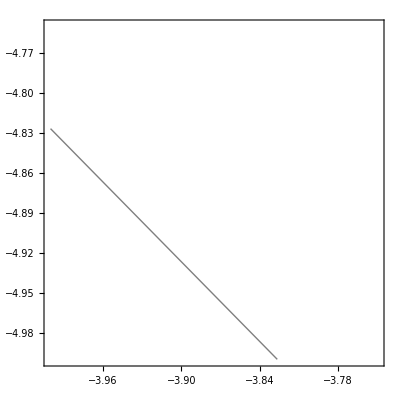

```mathematica
ListContourPlot[plotDataDoverHP3[[4]],Contours->{-2},ContourShading->None]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

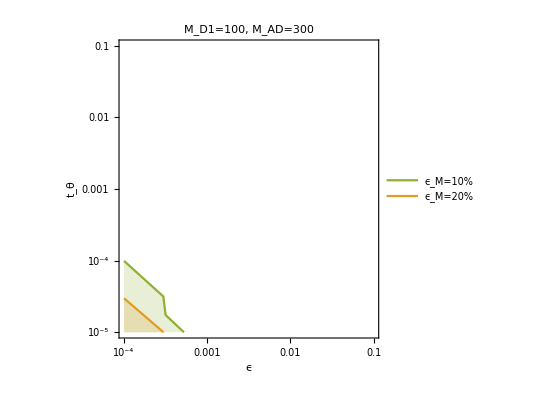

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig1=Map[ToLinearScale,%];
(*plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]*)
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig2=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverH[[3]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig3=Map[ToLinearScale,%];
(*Show[ListLogLogPlot[{fig1},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}],ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]]*)
ListLogLogPlot[{fig2,fig3},Joined->True,Filling->Bottom,PlotStyle->{colors[[3]],colors[[2]]},PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},PlotLabel->"M_D1=100, M_AD=300", Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"},PlotLegends->{"ϵ_M=10%","ϵ_M=20%"}]
Export["plots/acropolis_bounds_MD1_100_MZp_300.png",%];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

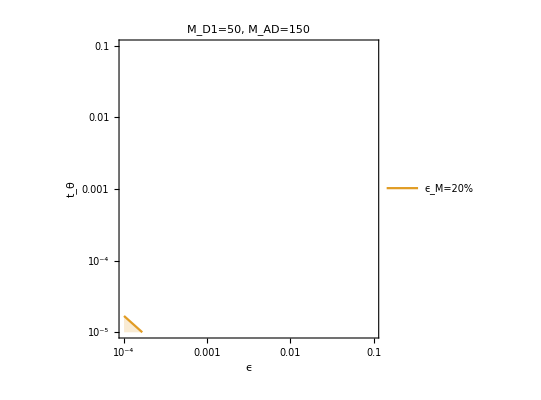

```mathematica
ListContourPlot[plotDataDoverHP2[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig1=Map[ToLinearScale,%];
(*plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]*)
ListContourPlot[plotDataDoverHP2[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig2=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverHP2[[3]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig3=Map[ToLinearScale,%];
(*Show[ListLogLogPlot[{fig1},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}],ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]]*)
ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotStyle->{colors[[2]],colors[[1]]},PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},PlotLabel->"M_D1=50, M_AD=150", Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"},PlotLegends->{"ϵ_M=20%","ϵ_M=30%"}]
Export["plots/acropolis_bounds_MD1_50_MZp_150.png",%];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

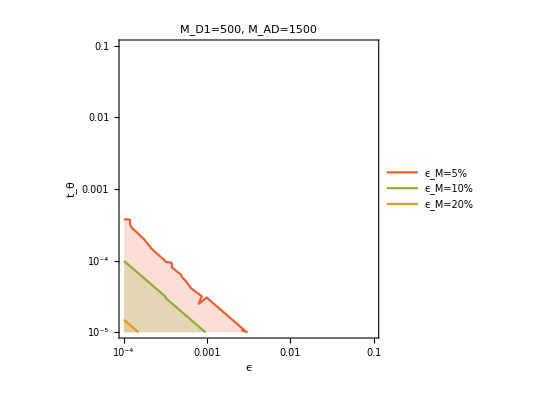

```mathematica
ListContourPlot[plotDataDoverHP3[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig1=Map[ToLinearScale,%];
(*plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]*)
ListContourPlot[plotDataDoverHP3[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig2=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverHP3[[3]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig3=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverHP3[[4]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig4=Map[ToLinearScale,%];
(*Show[ListLogLogPlot[{fig1},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}],ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]]*)
ListLogLogPlot[{fig2,fig3,fig4},Joined->True,Filling->Bottom,PlotStyle->{colors[[4]],colors[[3]],colors[[2]],colors[[1]]},PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},PlotLabel->"M_D1=500, M_AD=1500", Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"},PlotLegends->{"ϵ_M=5%","ϵ_M=10%","ϵ_M=20%","ϵ_M=30%"}]
Export["plots/acropolis_bounds_MD1_500_MZp_1500.png",%];
```

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig1=Map[ToLinearScale,%];
(*plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]*)
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig2=Map[ToLinearScale,%];
ListContourPlot[plotDataDoverH[[3]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
fig3=Map[ToLinearScale,%];
(*Show[ListLogLogPlot[{fig1},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}],ListLogLogPlot[{fig2},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]]*)
ListLogLogPlot[{fig2,fig3},Joined->True,Filling->Bottom,PlotStyle->{colors[[2]],colors[[3]]},PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},PlotLabel->"M_D1=100, M_AD=300", Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"},PlotLegends->{"ϵ_M=10%","ϵ_M=20%"}]
Export["acropolis_bounds_MD1_100_MZp_300.png",%];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

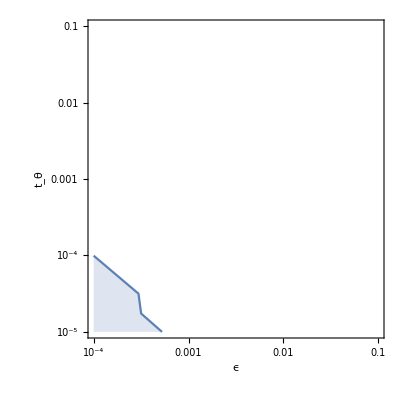

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 7 of {{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,«8»,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},«1»,{-«22»,«27»,0.}} does not exist.

Part::partw: Part 5 of {{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,«8»,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},«1»,{-«22»,«27»,0.}} does not exist.

Part::partw: Part 16 of {{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{-«21»,«27»,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{«1»}},«1»,{«1»}} cannot be transposed.

Part::take: Cannot take positions 1 through 2 in Transpose[{«1»}].

Part::pkspec1: The expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,«23»,Indeterminate,Indeterminate,Indeterminate},(-0.83+({{-4.,«27»,0.},{«1»},{«1»}}«1»«1»⟧)/({{«29»},{«29»},{«29»}}⟦5⟧))/(√(0.0225+Min[Abs[Plus[«2»]],Abs[Plus[«2»]]]^2))} cannot be used as a part specification.

Set::setps: Transpose[data] in the part assignment is not a symbol.

```mathematica
plotDataHe3overD
```

Transpose[Transpose[{{{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,0.,0.752573398598222809,0.0000179224799666167767,0.,7.83537461540709537×10^-6,0.061841799884810672,2.62699499510684072×10^-14,4.3759315918491923×10^-10,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},{-4.,-4.5,0.,0.752507899913477663,0.0000183792394586748446,0.,7.75538032924309804×10^-6,0.0618580099927989249,8.1047489990564829×10^-15,4.08745114368465401×10^-10,0.,0.,0.752573399913443186,0.0000179224794721278291,0.,7.835374629244539×10^-6,0.0618417999928008305,2.62699499969417764×10^-14,4.37593003606870924×10^-10,0.,0.,0.752442499913512419,0.0000188398194451093466,0.,7.68602713924149763×10^-6,0.0618741799927970404,1.26003799985331233×10^-15,3.82641264052551756×10^-10,0.},{-4.,-4.,0.,0.752507901774457366,0.0000183783472959809235,0.,7.7553804118285529×10^-6,0.0618580099991817844,8.10474899988206055×10^-15,4.08663319691643629×10^-10,0.,0.,0.752573401730085578,0.0000179216094814188252,0.,7.83537471788163939×10^-6,0.0618417999991880754,2.6269949999617722×10^-14,4.37505165408737694×10^-10,0.,0.,0.75244250181920036,0.0000188389049250005592,0.,7.68602721638142002×10^-6,0.0618741799991761043,1.26003799998166414×10^-15,3.82564907870762372×10^-10,0.},{-4.,-3.5,0.,0.752507906913517655,0.0000183757825567677652,0.,7.75538066344087403×10^-6,0.0618580100002209324,8.10474899998525776×10^-15,4.08411805071226833×10^-10,0.,0.,0.75257340674166906,0.0000179191084809828423,0.,7.8353749880788578×10^-6,0.0618418000002456045,2.62699499999522148×10^-14,4.37235066942472234×10^-10,0.,0.,0.752442507086803381,0.0000188362759139466319,0.,7.68602745126947033×10^-6,0.0618741800001987308,1.26003799999770799×10^-15,3.82330116605169784×10^-10,0.},{-4.,-3.,0.,0.752507900065645274,0.0000183792071345909545,0.,7.75538033772089157×10^-6,0.0618580100000006919,8.1047489999990786×10^-15,4.08737538233383778×10^-10,0.,0.,0.752573400064011633,0.0000179224479513605367,0.,7.83537463829147938×10^-6,0.0618418000000012652,2.62699499999970158×10^-14,4.37584867638074253×10^-10,0.,0.,0.752442500067292408,0.0000188397863109905154,0.,7.68602714720743422×10^-6,0.0618741800000001743,1.26003799999985685×10^-15,3.8263419169901068×10^-10,0.},{-3.5,-5.,0.,0.75250789991255429,0.0000183792399186942472,0.,7.75538032911869431×10^-6,0.0618580099927988,8.1047489990564829×10^-15,4.0874523872329765×10^-10,0.,0.,0.752573399912542795,0.0000179224799207148483,0.,7.83537462911094327×10^-6,0.0618417999928006917,2.62699499969417764×10^-14,4.37593137151168426×10^-10,0.,0.,0.752442499912565954,0.0000188398199166567388,0.,7.68602713912536771×10^-6,0.0618741799927969224,1.26003799985331233×10^-15,3.82641380138031297×10^-10,0.},{-3.5,-4.5,0.,0.75250790023934655,0.0000183791148516112686,0.,7.75538034138223722×10^-6,0.0618580099991113339,8.10474899988206055×10^-15,4.08733765998087981×10^-10,0.,0.,0.752573400233125245,0.0000179223579617930795,0.,7.83537464223028931×10^-6,0.0618417999991124276,2.6269949999617722×10^-14,4.37580816746371796×10^-10,0.,0.,0.752442500245619872,0.0000188396917154182106,0.,7.68602715061905085×10^-6,0.0618741799991103375,1.26003799998166414×10^-15,3.82630670229868103×10^-10,0.},{-3.5,-4.,0.,0.752507900946953856,0.0000183787658387375286,0.,7.75538037573978414×10^-6,0.061858009999933232,8.10474899998525776×10^-15,4.08699506161169532×10^-10,0.,0.,0.752573400923385982,0.0000179220176225707125,0.,7.83537467912027161×10^-6,0.0618417999999366502,2.62699499999522148×10^-14,4.37544025527088132×10^-10,0.,0.,0.752442500970718742,0.0000188393339563531519,0.,7.68602718269772338×10^-6,0.0618741799999301609,1.26003799999770799×10^-15,3.82598688350089377×10^-10,0.},{-3.5,-3.5,0.,0.752507900006573194,0.0000183792366705805856,0.,7.75538033080427124×10^-6,0.0618580099999937738,8.1047489999990786×10^-15,4.08744454852821326×10^-10,0.,0.,0.752573400006407711,0.0000179224767533231556,0.,7.83537463086375937×10^-6,0.0618417999999938406,2.62699499999970158×10^-14,4.37592295356964234×10^-10,0.,0.,0.752442500006740067,0.0000188398165871460164,0.,7.68602714075074262×10^-6,0.0618741799999937142,1.26003799999985685×10^-15,3.826406483917791×10^-10,0.},{-3.,-5.,0.,0.752507900023959508,0.0000183792225449462821,0.,7.75538033149053734×10^-6,0.0618580099991014459,8.10474899988206055×10^-15,4.08743657700757081×10^-10,0.,0.,0.752573400023091033,0.0000179224629787384451,0.,7.83537463160772704×10^-6,0.0618417999991018041,2.6269949999617722×10^-14,4.37591439312446637×10^-10,0.,0.,0.75244250002483537,0.0000188398021075261986,0.,7.68602714138504664×10^-6,0.0618741799991011088,1.26003799998166414×10^-15,3.82639904237025224×10^-10,0.},{-3.,-4.5,0.,0.752507900148997599,0.0000183791648168353452,0.,7.75538033716882429×10^-6,0.0618580099998946587,8.10474899998525776×10^-15,4.08738077120608074×10^-10,0.,0.,0.752573400145260529,0.000017922406685283779,0.,7.83537463769940165×10^-6,0.061841799999895225,2.62699499999522148×10^-14,4.37585446397364389×10^-10,0.,0.,0.752442500152765814,0.0000188397429327605929,0.,7.68602714669136246×10^-6,0.061874179999894155,1.26003799999770799×10^-15,3.82634694711738339×10^-10,0.},{-3.,-4.,0.,0.752507900001153973,0.0000183792393802003388,0.,7.75538033014474767×10^-6,0.0618580099999931146,8.1047489999990786×10^-15,4.08745114376278691×10^-10,0.,0.,0.752573400001123161,0.0000179224793956035659,0.,7.83537463015550091×10^-6,0.0618417999999931328,2.62699499999970158×10^-14,4.37593003615501106×10^-10,0.,0.,0.752442500001185066,0.0000188398193646682844,0.,7.68602714013507334×10^-6,0.0618741799999931036,1.26003799999985685×10^-15,3.82641264059655531×10^-10,0.},{-2.5,-5.,0.,0.752507900016745723,0.0000183792309427349958,0.,7.75538033085814084×10^-6,0.0618580099998883512,8.10474899998525776×10^-15,4.08744387803217456×10^-10,0.,0.,0.752573400016295357,0.0000179224711678257115,0.,7.83537463092243842×10^-6,0.0618417999998884527,2.62699499999522148×10^-14,4.37592223358858746×10^-10,0.,0.,0.752442500017199811,0.0000188398107157617829,0.,7.68602714080027881×10^-6,0.0618741799998882638,1.26003799999770799×10^-15,3.82640585795866196×10^-10,0.},{-2.5,-4.5,0.,0.752507900000223384,0.0000183792398455332739,0.,7.75538033003296982×10^-6,0.0618580099999930036,8.1047489999990786×10^-15,4.08745226153798552×10^-10,0.,0.,0.752573400000215553,0.0000179224798493720719,0.,7.83537463003546449×10^-6,0.0618417999999930079,2.62699499999970158×10^-14,4.3759312365275646×10^-10,0.,0.,0.752442500000231052,0.0000188398198416623695,0.,7.68602714003072904×10^-6,0.0618741799999929995,1.26003799999985685×10^-15,3.82641368404429227×10^-10,0.},{-2.,-5.,0.,0.752507899999936614,0.0000183792399889236801,0.,7.75538033000172616×10^-6,0.0618580099999929689,8.1047489999990786×10^-15,4.08745257397169019×10^-10,0.,0.,0.752573399999935999,0.0000179224799891989461,0.,7.83537463000191182×10^-6,0.0618417999999929732,2.62699499999970158×10^-14,4.37593157204834649×10^-10,0.,0.,0.752442499999937176,0.0000188398199886461096,0.,7.68602714000156231×10^-6,0.0618741799999929648,1.26003799999985685×10^-15,3.82641397570246302×10^-10,0.}},{{-4.,-5.,0.,0.75250963205863497,0.0000175131890979594588,0.,7.75539565411958412×10^-6,0.0618580100119359017,8.10855614809201138×10^-15,3.9320874091974502×10^-10,0.,0.,0.752575089012511356,0.0000170779521611662059,0.,7.83539108674137791×10^-6,0.061841800013071685,2.62738855181635309×10^-14,4.20921799268756917×10^-10,0.,0.,0.752444275464764445,0.0000179520660322053691,0.,7.68604144342321436×10^-6,0.0618741800109123413,1.26364689078768402×10^-15,3.68127505591210179×10^-10,0.},{-4.,-4.5,0.,0.752514765561995702,0.0000149464572815630341,0.,7.75544316996682342×10^-6,0.0618580100630680002,8.11608982663206855×10^-15,3.45227167654109903×10^-10,0.,0.,0.752580094939266919,0.0000145750086564448645,0.,7.8354421029771169×10^-6,0.0618418000677083274,2.62815865449324232×10^-14,3.6943486568652754×10^-10,0.,0.,0.752449537611686758,0.0000153210124268602792,0.,7.68608580493074749×10^-6,0.0618741800588865909,1.27081936608621367×10^-15,3.23304604180685772×10^-10,0.},{-4.,-4.,0.,0.752508364206120439,0.0000181471367711239886,0.,7.75538671141907302×10^-6,0.0618580100063549285,8.10478281445816242×10^-15,4.02362202218472318×10^-10,0.,0.,0.752573852669683352,0.0000176961449896074729,0.,7.83538148133453866×10^-6,0.0618418000068248694,2.6269985061236007×10^-14,4.30740169344241336×10^-10,0.,0.,0.752442975839039518,0.0000186019003115652697,0.,7.68603309836734313×10^-6,0.0618741800059318531,1.26007001532016076×10^-15,3.76681409108097582×10^-10,0.},{-4.,-3.5,0.,0.752507900003195895,0.000018379238380775241,0.,7.75538032998879366×10^-6,0.0618580099999965355,8.10475052673734201×10^-15,4.08745202898597235×10^-10,0.,0.,0.752573400003115345,0.0000179224784210185495,0.,7.83537462999226919×10^-6,0.0618417999999965468,2.62699516376758617×10^-14,4.37593098698774991×10^-10,0.,0.,0.752442500003277059,0.0000188398183401954601,0.,7.68602713998564487×10^-6,0.0618741799999965383,1.26003942589290413×10^-15,3.82641346680012022×10^-10,0.},{-3.5,-5.,0.,0.752508811236745845,0.0000179236190044470628,0.,7.75538860749385512×10^-6,0.0618580100079040851,8.10613265070272692×10^-15,4.00391092685669381×10^-10,0.,0.,0.752574288590599605,0.0000174781820784840423,0.,7.83538351746008438×10^-6,0.0618418000085149897,2.62713729170676118×10^-14,4.28628213326405903×10^-10,0.,0.,0.752443434072287531,0.0000183727812327739605,0.,7.68603486787874346×10^-6,0.0618741800073536533,1.26135224906624651×10^-15,3.74837555642945556×10^-10,0.},{-3.5,-4.5,0.,0.752507985259253442,0.0000183366102026582575,0.,7.75538146365409038×10^-6,0.0618580100011058148,8.10475503221975725×10^-15,4.0761131181892932×10^-10,0.,0.,0.752573483140385857,0.0000178809096363685703,0.,7.83537584710985226×10^-6,0.0618418000011892871,2.6269956198955551×10^-14,4.36375752931931638×10^-10,0.,0.,0.752442587395841467,0.0000187961219086349247,0.,7.68602819851858384×10^-6,0.0618741800010306695,1.26004373125469863×10^-15,3.81582590046598339×10^-10,0.},{-3.5,-4.,0.,0.752507900000383923,0.000018379239786711962,0.,7.75538032999875985×10^-6,0.0618580099999964869,8.10474920110656512×10^-15,4.08745252479422493×10^-10,0.,0.,0.752573400000373205,0.0000179224797920129015,0.,7.83537462999922164×10^-6,0.0618417999999964912,2.62699502157197078×10^-14,4.3759315192628259×10^-10,0.,0.,0.752442500000394587,0.0000188398197813666985,0.,7.68602713999834359×10^-6,0.0618741799999964898,1.26003818782303064×10^-15,3.82641392977455819×10^-10,0.},{-3.,-5.,0.,0.752507908420978922,0.0000183750293394704074,0.,7.75538044597769583×10^-6,0.0618580100000878791,8.10474961466144208×10^-15,4.08629250786397489×10^-10,0.,0.,0.752573408211692496,0.0000179183739826070491,0.,7.83537475451841813×10^-6,0.0618418000000964252,2.62699506374995294×10^-14,4.37468609731449147×10^-10,0.,0.,0.752442508632015561,0.0000188355038211766543,0.,7.68602724828875134×10^-6,0.0618741800000801798,1.26003858189490337×10^-15,3.82533080024420637×10^-10,0.},{-3.,-4.5,0.,0.75250790000005896,0.0000183792399491730744,0.,7.75538033000003718×10^-6,0.06185800999999648,8.10474903823239304×10^-15,4.08745257776349543×10^-10,0.,0.,0.752573400000056347,0.000017922479950436279,0.,7.83537463000017709×10^-6,0.0618417999999964843,2.62699500410094398×10^-14,4.37593157612572446×10^-10,0.,0.,0.752442500000061521,0.0000188398199478993017,0.,7.6860271399999106×10^-6,0.0618741799999964828,1.26003803570744476×10^-15,3.82641397923786088×10^-10,0.},{-2.5,-5.,0.,0.752507899999965257,0.0000183792399959915025,0.,7.75538032999971022×10^-6,0.06185800999999648,8.1047490036381192×10^-15,4.08745259852820207×10^-10,0.,0.,0.752573399999964976,0.0000179224799960911211,0.,7.83537462999971631×10^-6,0.0618417999999964843,2.62699500039019467×10^-14,4.37593159841991856×10^-10,0.,0.,0.752442499999965486,0.0000188398199958910399,0.,7.68602713999970562×10^-6,0.0618741799999964828,1.26003800339800319×10^-15,3.82641399862569386×10^-10,0.}},{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}}]⟦1;;2,{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},(-0.83+{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧)/(√(0.0225+(Min[Abs[{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧-{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦16⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦14⟧],Abs[{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧-{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦25⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦23⟧]])^2))}⟧]

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red,FrameLabel->{"ϵ","t_θ"}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

```mathematica
He4mean[data_]:=4*data[[8]];
He4high[data_]:=4*data[[17]];
He4low[data_]:=4*data[[26]];
He4obs=2.45*10^-1;
He4err=0.03*10^-1;
deltaHe4[mean_,high_,low_]:=(mean-He4obs)/Sqrt[sigmaTh[mean,high,low]^2+He4err^2];
plotDataHe4=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe4,Map[He4mean,data],Map[He4high,data],Map[He4low,data]]]];
```

Set::setps: Transpose[data] in the part assignment is not a symbol.

```mathematica
plotDataHe4
```

{{-4.,-5.,0.810492},{-4.,-4.5,0.810492},{-4.,-4.,0.810492},{-4.,-3.5,0.810492},{-3.5,-5.,0.810492},{-3.5,-4.5,0.810492},{-3.5,-4.,0.810492},{-3.,-5.,0.810492},{-3.,-4.5,0.810492},{-2.5,-5.,0.810492}}

```mathematica
ListContourPlot[plotDataHe4,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt4=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Darker[Green]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

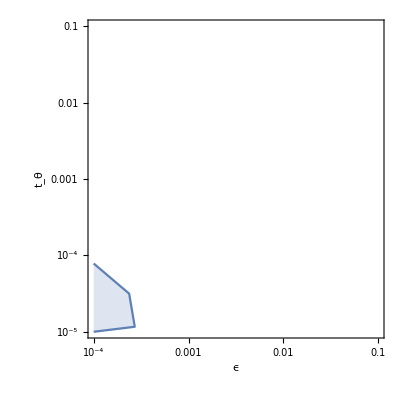

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

Part::partw: Part 2 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-«22»,-«22»,-«19»},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

Part::partw: Part 2 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListContourPlot::arrayerr: {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}}⟦2⟧ must be a valid array.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

Part::partw: Part 3 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-«22»,-«22»,-«19»},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

Part::partw: Part 3 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListContourPlot::arrayerr: {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}}⟦3⟧ must be a valid array.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

```mathematica
Show[plt1,plt2,plt3,plt4]
```

```mathematica
fig1
```

{10^({}⟦1⟧),10^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧

```mathematica
ListContourPlot[plotDataDoverH[[1]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Orange,FrameLabel->{"ϵ","t_θ"}]
ListContourPlot[plotDataDoverH[[2]],Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","t_θ"}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

Part::partw: Part 2 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-«22»,-«22»,-«19»},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

Part::partw: Part 2 of {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListContourPlot::arrayerr: {{{-4.,-5.,-1.48908},{-4.,-4.5,-1.4895},{-4.,-4.,-1.49017},{-4.,-3.5,-1.48908},{-3.5,-5.,-1.48913},{-3.5,-4.5,-1.48924},{-3.5,-4.,-1.48908},{-3.,-5.,-1.4891},{-3.,-4.5,-1.48908},{-2.5,-5.,-1.48908}}}⟦2⟧ must be a valid array.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 7 of {{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,«8»,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},«1»,{-«22»,«27»,0.}} does not exist.

Part::partw: Part 5 of {{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,«8»,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},«1»,{-«22»,«27»,0.}} does not exist.

Part::partw: Part 16 of {{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{-«21»,«27»,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{«1»}},«1»,{«1»}} cannot be transposed.

Part::take: Cannot take positions 1 through 2 in Transpose[{«1»}].

Part::pkspec1: The expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,«23»,Indeterminate,Indeterminate,Indeterminate},(-0.83+({{-4.,«27»,0.},{«1»},{«1»}}«1»«1»⟧)/({{«29»},{«29»},{«29»}}⟦5⟧))/(√(0.0225+Min[Abs[Plus[«2»]],Abs[Plus[«2»]]]^2))} cannot be used as a part specification.

Set::setps: Transpose[data] in the part assignment is not a symbol.

```mathematica
plotDataHe3overD
```

Transpose[Transpose[{{{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,0.,0.752573398598222809,0.0000179224799666167767,0.,7.83537461540709537×10^-6,0.061841799884810672,2.62699499510684072×10^-14,4.3759315918491923×10^-10,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},{-4.,-4.5,0.,0.752507899913477663,0.0000183792394586748446,0.,7.75538032924309804×10^-6,0.0618580099927989249,8.1047489990564829×10^-15,4.08745114368465401×10^-10,0.,0.,0.752573399913443186,0.0000179224794721278291,0.,7.835374629244539×10^-6,0.0618417999928008305,2.62699499969417764×10^-14,4.37593003606870924×10^-10,0.,0.,0.752442499913512419,0.0000188398194451093466,0.,7.68602713924149763×10^-6,0.0618741799927970404,1.26003799985331233×10^-15,3.82641264052551756×10^-10,0.},{-4.,-4.,0.,0.752507901774457366,0.0000183783472959809235,0.,7.7553804118285529×10^-6,0.0618580099991817844,8.10474899988206055×10^-15,4.08663319691643629×10^-10,0.,0.,0.752573401730085578,0.0000179216094814188252,0.,7.83537471788163939×10^-6,0.0618417999991880754,2.6269949999617722×10^-14,4.37505165408737694×10^-10,0.,0.,0.75244250181920036,0.0000188389049250005592,0.,7.68602721638142002×10^-6,0.0618741799991761043,1.26003799998166414×10^-15,3.82564907870762372×10^-10,0.},{-4.,-3.5,0.,0.752507906913517655,0.0000183757825567677652,0.,7.75538066344087403×10^-6,0.0618580100002209324,8.10474899998525776×10^-15,4.08411805071226833×10^-10,0.,0.,0.75257340674166906,0.0000179191084809828423,0.,7.8353749880788578×10^-6,0.0618418000002456045,2.62699499999522148×10^-14,4.37235066942472234×10^-10,0.,0.,0.752442507086803381,0.0000188362759139466319,0.,7.68602745126947033×10^-6,0.0618741800001987308,1.26003799999770799×10^-15,3.82330116605169784×10^-10,0.},{-4.,-3.,0.,0.752507900065645274,0.0000183792071345909545,0.,7.75538033772089157×10^-6,0.0618580100000006919,8.1047489999990786×10^-15,4.08737538233383778×10^-10,0.,0.,0.752573400064011633,0.0000179224479513605367,0.,7.83537463829147938×10^-6,0.0618418000000012652,2.62699499999970158×10^-14,4.37584867638074253×10^-10,0.,0.,0.752442500067292408,0.0000188397863109905154,0.,7.68602714720743422×10^-6,0.0618741800000001743,1.26003799999985685×10^-15,3.8263419169901068×10^-10,0.},{-3.5,-5.,0.,0.75250789991255429,0.0000183792399186942472,0.,7.75538032911869431×10^-6,0.0618580099927988,8.1047489990564829×10^-15,4.0874523872329765×10^-10,0.,0.,0.752573399912542795,0.0000179224799207148483,0.,7.83537462911094327×10^-6,0.0618417999928006917,2.62699499969417764×10^-14,4.37593137151168426×10^-10,0.,0.,0.752442499912565954,0.0000188398199166567388,0.,7.68602713912536771×10^-6,0.0618741799927969224,1.26003799985331233×10^-15,3.82641380138031297×10^-10,0.},{-3.5,-4.5,0.,0.75250790023934655,0.0000183791148516112686,0.,7.75538034138223722×10^-6,0.0618580099991113339,8.10474899988206055×10^-15,4.08733765998087981×10^-10,0.,0.,0.752573400233125245,0.0000179223579617930795,0.,7.83537464223028931×10^-6,0.0618417999991124276,2.6269949999617722×10^-14,4.37580816746371796×10^-10,0.,0.,0.752442500245619872,0.0000188396917154182106,0.,7.68602715061905085×10^-6,0.0618741799991103375,1.26003799998166414×10^-15,3.82630670229868103×10^-10,0.},{-3.5,-4.,0.,0.752507900946953856,0.0000183787658387375286,0.,7.75538037573978414×10^-6,0.061858009999933232,8.10474899998525776×10^-15,4.08699506161169532×10^-10,0.,0.,0.752573400923385982,0.0000179220176225707125,0.,7.83537467912027161×10^-6,0.0618417999999366502,2.62699499999522148×10^-14,4.37544025527088132×10^-10,0.,0.,0.752442500970718742,0.0000188393339563531519,0.,7.68602718269772338×10^-6,0.0618741799999301609,1.26003799999770799×10^-15,3.82598688350089377×10^-10,0.},{-3.5,-3.5,0.,0.752507900006573194,0.0000183792366705805856,0.,7.75538033080427124×10^-6,0.0618580099999937738,8.1047489999990786×10^-15,4.08744454852821326×10^-10,0.,0.,0.752573400006407711,0.0000179224767533231556,0.,7.83537463086375937×10^-6,0.0618417999999938406,2.62699499999970158×10^-14,4.37592295356964234×10^-10,0.,0.,0.752442500006740067,0.0000188398165871460164,0.,7.68602714075074262×10^-6,0.0618741799999937142,1.26003799999985685×10^-15,3.826406483917791×10^-10,0.},{-3.,-5.,0.,0.752507900023959508,0.0000183792225449462821,0.,7.75538033149053734×10^-6,0.0618580099991014459,8.10474899988206055×10^-15,4.08743657700757081×10^-10,0.,0.,0.752573400023091033,0.0000179224629787384451,0.,7.83537463160772704×10^-6,0.0618417999991018041,2.6269949999617722×10^-14,4.37591439312446637×10^-10,0.,0.,0.75244250002483537,0.0000188398021075261986,0.,7.68602714138504664×10^-6,0.0618741799991011088,1.26003799998166414×10^-15,3.82639904237025224×10^-10,0.},{-3.,-4.5,0.,0.752507900148997599,0.0000183791648168353452,0.,7.75538033716882429×10^-6,0.0618580099998946587,8.10474899998525776×10^-15,4.08738077120608074×10^-10,0.,0.,0.752573400145260529,0.000017922406685283779,0.,7.83537463769940165×10^-6,0.061841799999895225,2.62699499999522148×10^-14,4.37585446397364389×10^-10,0.,0.,0.752442500152765814,0.0000188397429327605929,0.,7.68602714669136246×10^-6,0.061874179999894155,1.26003799999770799×10^-15,3.82634694711738339×10^-10,0.},{-3.,-4.,0.,0.752507900001153973,0.0000183792393802003388,0.,7.75538033014474767×10^-6,0.0618580099999931146,8.1047489999990786×10^-15,4.08745114376278691×10^-10,0.,0.,0.752573400001123161,0.0000179224793956035659,0.,7.83537463015550091×10^-6,0.0618417999999931328,2.62699499999970158×10^-14,4.37593003615501106×10^-10,0.,0.,0.752442500001185066,0.0000188398193646682844,0.,7.68602714013507334×10^-6,0.0618741799999931036,1.26003799999985685×10^-15,3.82641264059655531×10^-10,0.},{-2.5,-5.,0.,0.752507900016745723,0.0000183792309427349958,0.,7.75538033085814084×10^-6,0.0618580099998883512,8.10474899998525776×10^-15,4.08744387803217456×10^-10,0.,0.,0.752573400016295357,0.0000179224711678257115,0.,7.83537463092243842×10^-6,0.0618417999998884527,2.62699499999522148×10^-14,4.37592223358858746×10^-10,0.,0.,0.752442500017199811,0.0000188398107157617829,0.,7.68602714080027881×10^-6,0.0618741799998882638,1.26003799999770799×10^-15,3.82640585795866196×10^-10,0.},{-2.5,-4.5,0.,0.752507900000223384,0.0000183792398455332739,0.,7.75538033003296982×10^-6,0.0618580099999930036,8.1047489999990786×10^-15,4.08745226153798552×10^-10,0.,0.,0.752573400000215553,0.0000179224798493720719,0.,7.83537463003546449×10^-6,0.0618417999999930079,2.62699499999970158×10^-14,4.3759312365275646×10^-10,0.,0.,0.752442500000231052,0.0000188398198416623695,0.,7.68602714003072904×10^-6,0.0618741799999929995,1.26003799999985685×10^-15,3.82641368404429227×10^-10,0.},{-2.,-5.,0.,0.752507899999936614,0.0000183792399889236801,0.,7.75538033000172616×10^-6,0.0618580099999929689,8.1047489999990786×10^-15,4.08745257397169019×10^-10,0.,0.,0.752573399999935999,0.0000179224799891989461,0.,7.83537463000191182×10^-6,0.0618417999999929732,2.62699499999970158×10^-14,4.37593157204834649×10^-10,0.,0.,0.752442499999937176,0.0000188398199886461096,0.,7.68602714000156231×10^-6,0.0618741799999929648,1.26003799999985685×10^-15,3.82641397570246302×10^-10,0.}},{{-4.,-5.,0.,0.75250963205863497,0.0000175131890979594588,0.,7.75539565411958412×10^-6,0.0618580100119359017,8.10855614809201138×10^-15,3.9320874091974502×10^-10,0.,0.,0.752575089012511356,0.0000170779521611662059,0.,7.83539108674137791×10^-6,0.061841800013071685,2.62738855181635309×10^-14,4.20921799268756917×10^-10,0.,0.,0.752444275464764445,0.0000179520660322053691,0.,7.68604144342321436×10^-6,0.0618741800109123413,1.26364689078768402×10^-15,3.68127505591210179×10^-10,0.},{-4.,-4.5,0.,0.752514765561995702,0.0000149464572815630341,0.,7.75544316996682342×10^-6,0.0618580100630680002,8.11608982663206855×10^-15,3.45227167654109903×10^-10,0.,0.,0.752580094939266919,0.0000145750086564448645,0.,7.8354421029771169×10^-6,0.0618418000677083274,2.62815865449324232×10^-14,3.6943486568652754×10^-10,0.,0.,0.752449537611686758,0.0000153210124268602792,0.,7.68608580493074749×10^-6,0.0618741800588865909,1.27081936608621367×10^-15,3.23304604180685772×10^-10,0.},{-4.,-4.,0.,0.752508364206120439,0.0000181471367711239886,0.,7.75538671141907302×10^-6,0.0618580100063549285,8.10478281445816242×10^-15,4.02362202218472318×10^-10,0.,0.,0.752573852669683352,0.0000176961449896074729,0.,7.83538148133453866×10^-6,0.0618418000068248694,2.6269985061236007×10^-14,4.30740169344241336×10^-10,0.,0.,0.752442975839039518,0.0000186019003115652697,0.,7.68603309836734313×10^-6,0.0618741800059318531,1.26007001532016076×10^-15,3.76681409108097582×10^-10,0.},{-4.,-3.5,0.,0.752507900003195895,0.000018379238380775241,0.,7.75538032998879366×10^-6,0.0618580099999965355,8.10475052673734201×10^-15,4.08745202898597235×10^-10,0.,0.,0.752573400003115345,0.0000179224784210185495,0.,7.83537462999226919×10^-6,0.0618417999999965468,2.62699516376758617×10^-14,4.37593098698774991×10^-10,0.,0.,0.752442500003277059,0.0000188398183401954601,0.,7.68602713998564487×10^-6,0.0618741799999965383,1.26003942589290413×10^-15,3.82641346680012022×10^-10,0.},{-3.5,-5.,0.,0.752508811236745845,0.0000179236190044470628,0.,7.75538860749385512×10^-6,0.0618580100079040851,8.10613265070272692×10^-15,4.00391092685669381×10^-10,0.,0.,0.752574288590599605,0.0000174781820784840423,0.,7.83538351746008438×10^-6,0.0618418000085149897,2.62713729170676118×10^-14,4.28628213326405903×10^-10,0.,0.,0.752443434072287531,0.0000183727812327739605,0.,7.68603486787874346×10^-6,0.0618741800073536533,1.26135224906624651×10^-15,3.74837555642945556×10^-10,0.},{-3.5,-4.5,0.,0.752507985259253442,0.0000183366102026582575,0.,7.75538146365409038×10^-6,0.0618580100011058148,8.10475503221975725×10^-15,4.0761131181892932×10^-10,0.,0.,0.752573483140385857,0.0000178809096363685703,0.,7.83537584710985226×10^-6,0.0618418000011892871,2.6269956198955551×10^-14,4.36375752931931638×10^-10,0.,0.,0.752442587395841467,0.0000187961219086349247,0.,7.68602819851858384×10^-6,0.0618741800010306695,1.26004373125469863×10^-15,3.81582590046598339×10^-10,0.},{-3.5,-4.,0.,0.752507900000383923,0.000018379239786711962,0.,7.75538032999875985×10^-6,0.0618580099999964869,8.10474920110656512×10^-15,4.08745252479422493×10^-10,0.,0.,0.752573400000373205,0.0000179224797920129015,0.,7.83537462999922164×10^-6,0.0618417999999964912,2.62699502157197078×10^-14,4.3759315192628259×10^-10,0.,0.,0.752442500000394587,0.0000188398197813666985,0.,7.68602713999834359×10^-6,0.0618741799999964898,1.26003818782303064×10^-15,3.82641392977455819×10^-10,0.},{-3.,-5.,0.,0.752507908420978922,0.0000183750293394704074,0.,7.75538044597769583×10^-6,0.0618580100000878791,8.10474961466144208×10^-15,4.08629250786397489×10^-10,0.,0.,0.752573408211692496,0.0000179183739826070491,0.,7.83537475451841813×10^-6,0.0618418000000964252,2.62699506374995294×10^-14,4.37468609731449147×10^-10,0.,0.,0.752442508632015561,0.0000188355038211766543,0.,7.68602724828875134×10^-6,0.0618741800000801798,1.26003858189490337×10^-15,3.82533080024420637×10^-10,0.},{-3.,-4.5,0.,0.75250790000005896,0.0000183792399491730744,0.,7.75538033000003718×10^-6,0.06185800999999648,8.10474903823239304×10^-15,4.08745257776349543×10^-10,0.,0.,0.752573400000056347,0.000017922479950436279,0.,7.83537463000017709×10^-6,0.0618417999999964843,2.62699500410094398×10^-14,4.37593157612572446×10^-10,0.,0.,0.752442500000061521,0.0000188398199478993017,0.,7.6860271399999106×10^-6,0.0618741799999964828,1.26003803570744476×10^-15,3.82641397923786088×10^-10,0.},{-2.5,-5.,0.,0.752507899999965257,0.0000183792399959915025,0.,7.75538032999971022×10^-6,0.06185800999999648,8.1047490036381192×10^-15,4.08745259852820207×10^-10,0.,0.,0.752573399999964976,0.0000179224799960911211,0.,7.83537462999971631×10^-6,0.0618417999999964843,2.62699500039019467×10^-14,4.37593159841991856×10^-10,0.,0.,0.752442499999965486,0.0000188398199958910399,0.,7.68602713999970562×10^-6,0.0618741799999964828,1.26003800339800319×10^-15,3.82641399862569386×10^-10,0.}},{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}}]⟦1;;2,{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},(-0.83+{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧)/(√(0.0225+(Min[Abs[{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧-{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦16⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦14⟧],Abs[{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦7⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦5⟧-{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦25⟧/{{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,0.,0.752581768238117177,0.0000137387436379909744,0.,7.83519617423456191×10^-6,0.061841800077017374,3.15389369753920893×10^-14,3.60458029373994031×10^-10,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},{-4.,-4.5,0.,0.752507907786093555,0.000018375346885090706,0.,7.75538049359985155×10^-6,0.0618580100001611608,8.10493905479255452×10^-15,4.08570031597412627×10^-10,0.,0.,0.75257340759259006,0.0000179186836369903912,0.,7.83537480640846794×10^-6,0.0618418000001741061,2.6270153839656838×10^-14,4.37405000878201217×10^-10,0.,0.,0.752442507981215369,0.0000188358293240465074,0.,7.6860272920680541×10^-6,0.0618741800001495271,1.26021556750637222×10^-15,3.82477809536044188×10^-10,0.},{-3.5,-5.,0.,0.752507900391261364,0.0000183790442853342749,0.,7.75538033896627056×10^-6,0.0618580099999959457,8.10476587103980871×10^-15,4.08735247183758617×10^-10,0.,0.,0.752573400381533531,0.0000179222891492611672,0.,7.83537463969436245×10^-6,0.0618417999999966994,2.62699680951388536×10^-14,4.37582408107870242×10^-10,0.,0.,0.752442500401070635,0.0000188396193807305799,0.,7.68602714831065567×10^-6,0.0618741799999952824,1.26005376269259679×10^-15,3.82632052347931058×10^-10,0.}}⟦23⟧]])^2))}⟧]

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Bottom,PlotRange->{{10^-4,10^-1},{10^-5,10^-1}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red,FrameLabel->{"ϵ","t_θ"}]
```

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Part::pkspec1: The expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,«23»,Indeterminate,Indeterminate,Indeterminate},(-0.83+({{-4.,«27»,0.},{«1»},{«1»}}«1»«1»⟧)/({{«29»},{«29»},{«29»}}⟦5⟧))/(√(0.0225+Min[Abs[Plus[«2»]],Abs[Plus[«2»]]]^2))} cannot be used as a part specification.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Part::pkspec1: The expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,«23»,Indeterminate,Indeterminate,Indeterminate},(-0.83+({{-4.,«27»,0.},{«1»},{«1»}}«1»«1»⟧)/({{«29»},{«29»},{«29»}}⟦5⟧))/(√(0.0225+Min[Abs[Plus[«2»]],Abs[Plus[«2»]]]^2))} cannot be used as a part specification.

ListContourPlot::arrayerr: Transpose[Transpose[{{{-4.,-5.,0.,0.752508,0.0000183792,0.,7.75538×10^-6,0.061858,8.10475×10^-15,4.08745×10^-10,0.,0.,0.752573,0.0000179225,0.,7.83537×10^-6,0.0618418,2.62699×10^-14,4.37593×10^-10,0.,0.,0.752442,0.0000188398,0.,7.68603×10^-6,0.0618742,1.26004×10^-15,3.82641×10^-10,0.},«13»,{-2.,-5.,0.,0.752508,0.0000183792,«20»,0.0618742,1.26004×10^-15,3.82641×10^-10,0.}},{«1»},{«1»}}]⟦«1»⟧] must be a valid array.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

-Graphics-

```mathematica
He4mean[data_]:=4*data[[8]];
He4high[data_]:=4*data[[17]];
He4low[data_]:=4*data[[26]];
He4obs=2.45*10^-1;
He4err=0.03*10^-1;
deltaHe4[mean_,high_,low_]:=(mean-He4obs)/Sqrt[sigmaTh[mean,high,low]^2+He4err^2];
plotDataHe4=Transpose[AppendTo[Transpose[data][[1;;2]],Map3[deltaHe4,Map[He4mean,data],Map[He4high,data],Map[He4low,data]]]];
```

Part::partw: Part 8 of {{-4.,-5.,0.,0.752516481493869738,0.0000140888717469335401,0.,7.75519932587278092×10^-6,0.0618580100717924936,1.30185811918162047×10^-14,3.36835326507621355×10^-10,0.,«8»,0.,0.,0.752451296533594438,0.0000144419283905844117,0.,7.68584375395597066×10^-6,0.0618741800670813344,5.85004871679951864×10^-15,3.1544292322456652×10^-10,0.},«1»,{-«22»,«27»,0.}} does not exist.

Part::partw: Part 17 of {{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{-«21»,«27»,0.}} does not exist.

Part::partw: Part 17 of {{-4.,-5.,0.,0.75250963205863497,0.0000175131890979594588,0.,7.75539565411958412×10^-6,0.0618580100119359017,8.10855614809201138×10^-15,3.9320874091974502×10^-10,0.,«8»,0.,0.,0.752444275464764445,0.0000179520660322053691,0.,7.68604144342321436×10^-6,0.0618741800109123413,1.26364689078768402×10^-15,3.68127505591210179×10^-10,0.},«8»,{-«21»,«27»,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{{-4.,-5.,0.,0.752507898598344771,0.0000183792399657659992,0.,7.75538031555615014×10^-6,0.0618580098847804766,8.1047489849037282×10^-15,4.08745259238652613×10^-10,0.,«8»,0.,0.,0.75244249859846668,0.0000188398199649080994,0.,7.68602712568538752×10^-6,0.0618741798847503577,1.26003799765299644×10^-15,3.82641399287274834×10^-10,0.},«13»,{«1»}},«1»,{«1»}} cannot be transposed.

Part::take: Cannot take positions 1 through 2 in Transpose[{«1»}].

Part::pkspec1: The expression {{Divide[-14.245, Power[9. Power[10, -6] + Power[Min[Abs[-16.00000000000000000 - 4 {<<15>>}[[17]]], <<41>>], 2], <<1>>]], <<27>>, Divide[<<2>>]}, <<2>>} cannot be used as a part specification.

Set::setps: Transpose[data] in the part assignment is not a symbol.

Part::pkspec1: The expression {{Divide[-14.245, Power[9. Power[10, -6] + Power[Min[Abs[-16.00000000000000000 - 4 {<<15>>}[[17]]], <<41>>], 2], <<1>>]], <<27>>, Divide[<<2>>]}, <<2>>} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
plotDataHe4
```

Part::pkspec1: The expression {{Divide[-14.245, Power[9. Power[10, -6] + Power[Min[Abs[-16.00000000000000000 - 4 {<<15>>}[[17]]], <<41>>], 2], <<1>>]], <<27>>, Divide[<<2>>]}, <<2>>} cannot be used as a part specification.

Transpose[Transpose[{1}]⟦1;;2,{1}⟧]
 |  |  |  |

```mathematica
ListContourPlot[plotDataHe4,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt4=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Darker[Green]]
```

Part::pkspec1: The expression {{Divide[-14.245, Power[9. Power[10, -6] + Power[Min[Abs[-16.00000000000000000 - 4 {<<15>>}[[17]]], <<41>>], 2], <<1>>]], <<27>>, Divide[<<2>>]}, <<2>>} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

ListContourPlot::arrayerr: Transpose[Transpose[{{{-4., -5., 0., 0.752508, 0.0000183792, 0., <<20>>, 1.26004 Power[<<2>>], 3.82641 Power[10, -10], 0.}, <<14>>}, <<2>>}][[<<2>>]]] must be a valid array.

Part::pkspec1: The expression {{Divide[-14.245, Power[9. Power[10, -6] + Power[Min[Abs[-16.00000000000000000 - 4 {<<15>>}[[17]]], <<41>>], 2], <<1>>]], <<27>>, Divide[<<2>>]}, <<2>>} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

ListContourPlot::arrayerr: Transpose[Transpose[{{{-4., -5., 0., 0.752508, 0.0000183792, 0., <<20>>, 1.26004 Power[<<2>>], 3.82641 Power[10, -10], 0.}, <<14>>}, <<2>>}][[<<2>>]]] must be a valid array.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListContourPlot::arrayerr: Transpose[Transpose[{{{-4., -5., 0., 0.752508, 0.0000183792, 0., <<20>>, 1.26004 Power[<<2>>], 3.82641 Power[10, -10], 0.}, <<14>>}, <<2>>}][[<<2>>]]] must be a valid array.

General::stop: Further output of ListContourPlot::arrayerr will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

```mathematica
Show[plt1,plt2,plt3,plt4]
```

-Graphics-

### Test by comparing with monochromatic source term

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst_1.dat"];
```

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
Map3[func_,list1_,list2_,list3_]:=If[Length[list1]==Length[list2]&&Length[list1]==Length[list3],Table[func[list1[[i]],list2[[i]],list3[[i]]],{i,1,Length[list1]}],{}];
sigmaTh[mean_,high_,low_]:=Min[Abs[mean-high],Abs[mean-low]];
```

```mathematica
DoverHmean[data_]:=data[[5]]/data[[4]];
DoverHhigh[data_]:=data[[14]]/data[[13]];
DoverHlow[data_]:=data[[23]]/data[[22]];
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
deltaDoverH[mean_,high_,low_]:=(mean-DoverHobs)/Sqrt[sigmaTh[mean,high,low]^2+DoverHerr^2];
plotDataDoverH=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaDoverH,Map[DoverHmean,data],Map[DoverHhigh,data],Map[DoverHlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {10^(1⟦1⟧),10^(1⟦2⟧)} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogLogPlot::lpn: {10.^({}⟦1⟧),10.^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot[{10^({}⟦1⟧),10^({}⟦2⟧)}⟦{10^(1⟦1⟧),10^(1⟦2⟧)}⟧,Joined→True,Filling→Top,PlotRange→{{1/10000000000,1/10000},{1/1000000000000,1/1000}},Frame→True,AspectRatio→1,LabelStyle→Larger,FrameLabel→{ϵ,n_ϕ/n_γ},PlotLabel→D/H upper limit,PlotStyle→RGBColor[1, 0.5, 0]]

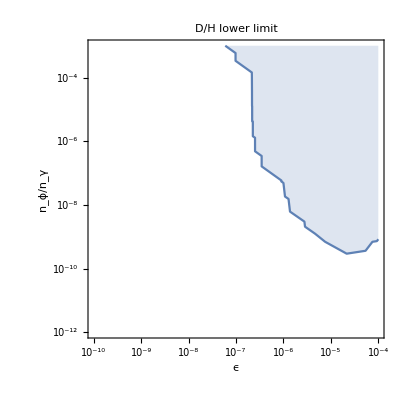

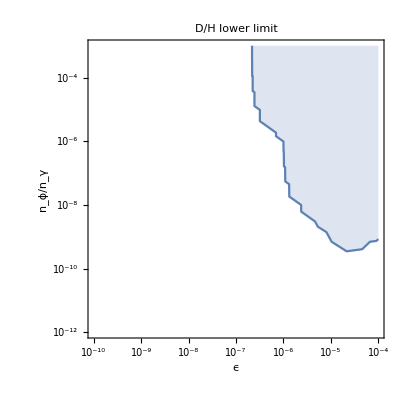

```mathematica
ListContourPlot[plotDataDoverH,Contours->{2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[%,Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->"D/H upper limit",PlotStyle->Orange]
ListContourPlot[plotDataDoverH,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[%,Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->"D/H lower limit"]
```

```mathematica
He3overDmean[data_]:=data[[7]]/data[[5]];
He3overDhigh[data_]:=data[[16]]/data[[14]];
He3overDlow[data_]:=data[[25]]/data[[23]];
He3overDobs=0.83;
He3overDerr=0.15;
deltaHe3overD[mean_,high_,low_]:=(mean-He3overDobs)/Sqrt[sigmaTh[mean,high,low]^2+He3overDerr^2];
plotDataHe3overD=Transpose[AppendTo[Log10[Transpose[data]][[1;;2]],Map3[deltaHe3overD,Map[He3overDmean,data],Map[He3overDhigh,data],Map[He3overDlow,data]]]];
```

Set::setps: Log10[Transpose[data]] in the part assignment is not a symbol.

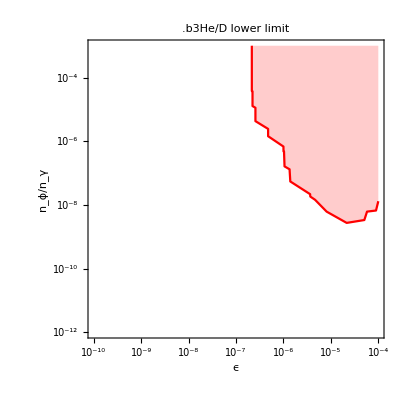

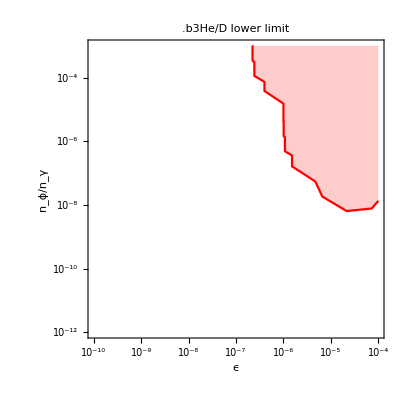

```mathematica
ListContourPlot[plotDataHe3overD,Contours->{-2},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt3=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^-10,10^-4},{10^-12,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red,FrameLabel->{"ϵ","n_ϕ/n_γ"},PlotLabel->".b3He/D lower limit"]
```

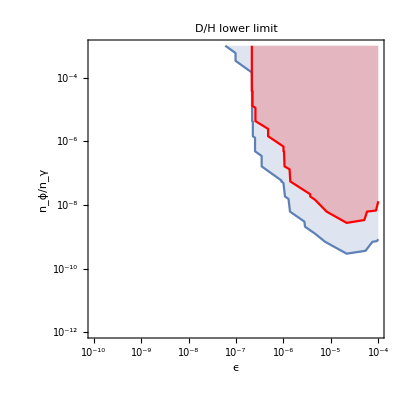

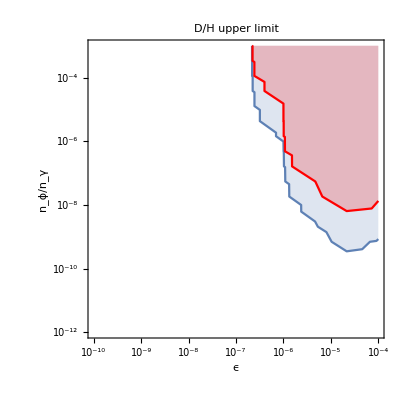

```mathematica
Show[plt2,plt3]
```